```mathematica
L[n_, 0] := 1
L[n_, 1] := L[n,1] = Sum[ Log[j],{j,2,n}]
L[n_, k_] := L[n,k] = Sum[ L[Floor[n/j], k-1], {j,2,n}]
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
ll[n_, z_] := N[Sum[ bins[ z,k] L[n,k],{k,0,Log[2,n]}]]
zeros[n_] := zeros[n] = List@@NRoots[ll[n,z]==0,z][[All,2]]
zs[n_] := zs[n] = List@@NRoots[ll[n,z]==0,z][[All,2]]
lp[n_] := 1-Product[ 1+1/r,{r,zs[n]}]
```

```mathematica
N[1-ll[100,-1]]
```

94.0453

```mathematica
zs[100]
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.66756,-3.06482-2.95324 ⅈ,-3.06482+2.95324 ⅈ,-0.00522175}

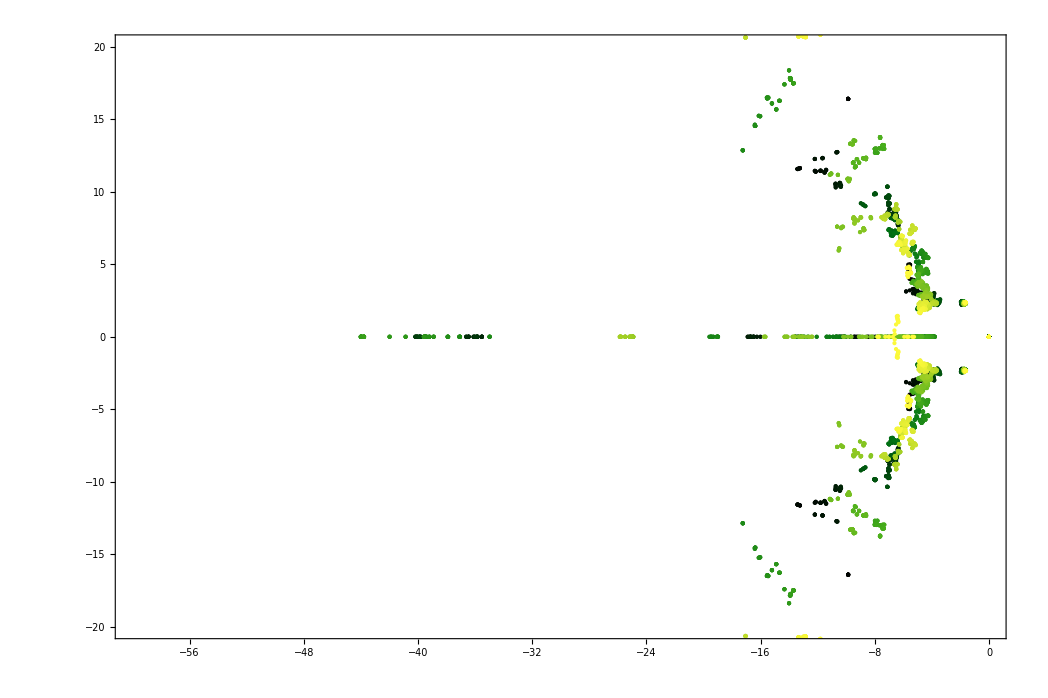

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 1000;bb = 1000;
pts=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zs[n],{n,aa,aa+bb}];
Graphics[pts,Frame->True,PlotRange->{{-60,0},{-20,20}}]
```